```mathematica
亥姆霍兹线圈的磁力线分布——折线法
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {6.2831611214131084832670761514128443536719714757055044174194335938}. NIntegrate obtained -6.08237×10^-17 and 4.23635×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {1.25163}. NIntegrate obtained 8.32667×10^-17 and 1.92294×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {4.43004}. NIntegrate obtained 3.81639×10^-17 and 1.88559×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

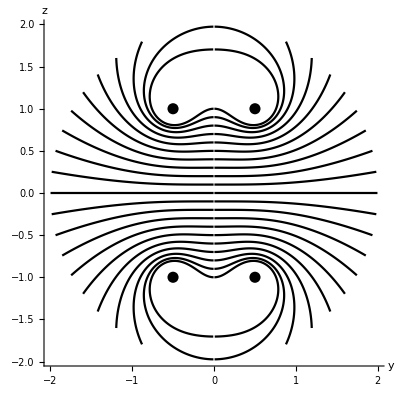

```mathematica
R=1.0;d=R;forceline={};
By0[y_,z_]:=
NIntegrate[(R*z*Sin[φ])/((z^2+y^2+R^2-2R*y*Sin[φ])^(3/2)),
{φ,0,2π}];
Bz0[y_,z_]:=
NIntegrate[(R*(R-y*Sin[φ]))/((z^2+y^2+R^2-2R*y*Sin[φ])^(3/2)),
{φ,0,2π}];
By[y_,z_]:=By0[y,z-d/2]+By0[y,z+d/2];
Bz[y_,z_]:=Bz0[y,z-d/2]+Bz0[y,z+d/2];
step=0.005R;r1=step;r2=2R;
Do[
θ=0;p={r1,y0};single={p};
While[(Abs[p[[1]]]>=r1)∧(Norm[p]<r2),
AppendTo[single,p];
p=p+step*{Cos[θ],Sin[θ]};
θ=Arg[Bz[p[[2]],p[[1]]]
+ⅈ*By[p[[2]],p[[1]]]]];
AppendTo[forceline,single];m=Length[single];
single=
Table[{-single[[j,1]],single[[j,2]]},{j,m}];
AppendTo[forceline,single],{y0,-R,R,0.1R}]
Show[
Graphics[{Thickness[0.004],Line/@forceline}],
Axes->True,AxesLabel->{"y","z"},
AxesStyle->Thickness[0.003],AspectRatio->1,
Epilog->{PointSize[0.02],
Point/@{{d/2,-R},{d/2,R},
{-d/2,R},{-d/2,-R}}}]
Clear[By0,Bz0,By,Bz]
```